```mathematica
weights = <|"a"->16,"b"->3,"c"->9,"d"->13,"e"->10,"f"->20,"g"->12,"h"->2,"i"->15,"j"->11,"k"->6,"l"->8,"m"->5,"n"->18,"o"->4,"p"->7,"q"->14,"r"->19,"s"->17,"t"->1|>
```

<|a→16,b→3,c→9,d→13,e→10,f→20,g→12,h→2,i→15,j→11,k→6,l→8,m→5,n→18,o→4,p→7,q→14,r→19,s→17,t→1|>

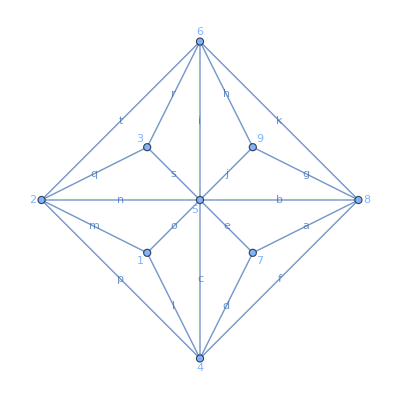

```mathematica
spanningTreesGraph=EdgeTaggedGraph[
Range[9],
{
7<->8, 8<->5, 5 <->4, 4<->7, 7<->5, 4<->8, 8<->9, 9<->6, 6<->5, 5<->9, 8<->6, 1<->4, 1<->2, 2<->5, 1<->5, 2<->4, 2<->3, 3<->6, 3<->5, 2<->6
}->CharacterRange["a","t"],
EdgeWeight->Values[weights],
EdgeLabels->"EdgeTag",VertexLabels->"Name",GraphLayout->{"TutteEmbedding","Rotation"->90Degree}
]
```

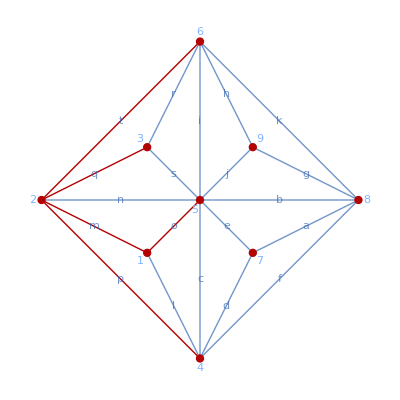

```mathematica
HighlightGraph[spanningTreesGraph, FindSpanningTree[spanningTreesGraph]]
```

```mathematica
edges = EdgeTags[FindSpanningTree[spanningTreesGraph]]
sortedEdges = KeySelect[weights, MemberQ[edges, #] &]//Sort
```

{m,o,q,p,t,e,b,h}

<|t→1,h→2,b→3,o→4,m→5,p→7,e→10,q→14|>

Shown here is helper for Kruskal’s Algorithm

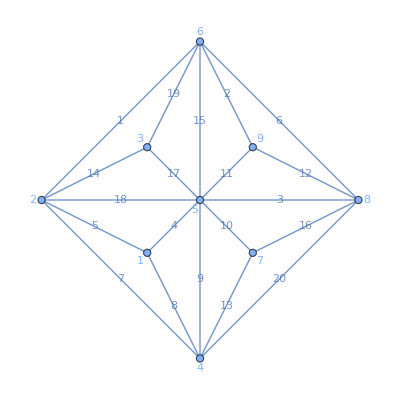

```mathematica
primSpanningTreeGraph = EdgeTaggedGraph[
Range[9],
{
7<->8, 8<->5, 5 <->4, 4<->7, 7<->5, 4<->8, 8<->9, 9<->6, 6<->5, 5<->9, 8<->6, 1<->4, 1<->2, 2<->5, 1<->5, 2<->4, 2<->3, 3<->6, 3<->5, 2<->6
}->CharacterRange["a","t"],
EdgeWeight->Values[weights],
EdgeLabels->"EdgeWeight",VertexLabels->"Name",GraphLayout->{"TutteEmbedding","Rotation"->90Degree}
]
```

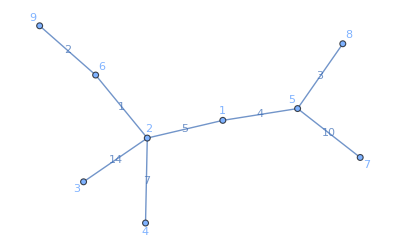

```mathematica
Graph[FindSpanningTree[primSpanningTreeGraph], GraphLayout->"SpringEmbedding"]
```

```mathematica
edges = EdgeTags[FindSpanningTree[primSpanningTreeGraph]]
```

{m,o,q,p,t,e,b,h}

```mathematica
weightedEdges = KeySelect[weights, MemberQ[edges, #] &]//Sort
```

<|t→1,h→2,b→3,o→4,m→5,p→7,e→10,q→14|>